# Code to Plot Numerical E-Field

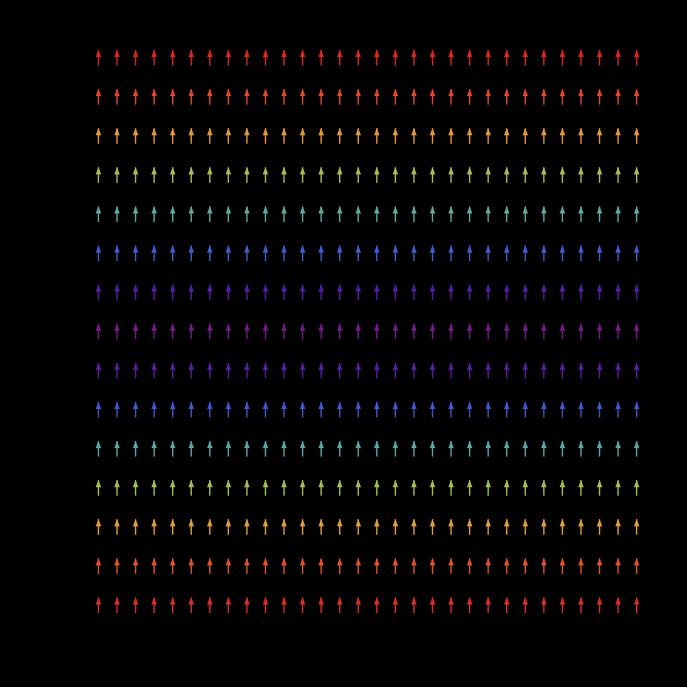

```mathematica
ClearAll["Global`*"]

data = Import["electricField.dat","Table"];
coords = data[[All,{1,2}]];
comps = data[[All,{3,4}]];
out = Thread[{coords,comps}];

eField = ListVectorPlot[out,
VectorScale->{0.02,Automatic,None},
VectorStyle->Thick,
VectorPoints->{30,15},
VectorColorFunctionScaling->True,
VectorColorFunction->"Rainbow",
PlotLegends->BarLegend[{"Rainbow"}], 
Background->Black, 
PerformanceGoal->"Quality",
AspectRatio->1
]
```

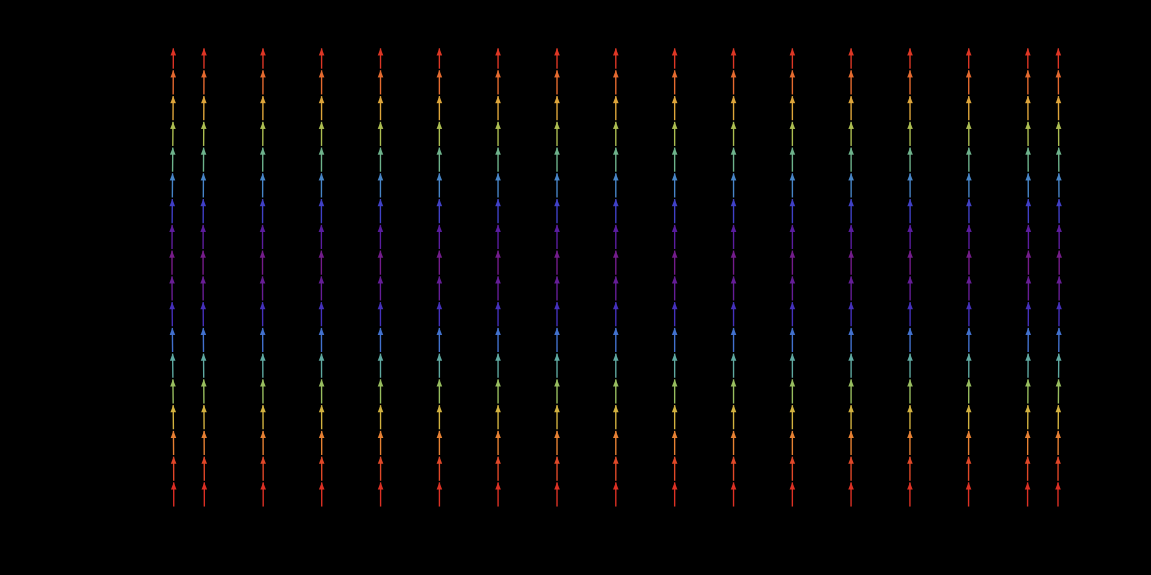

```mathematica
ListStreamPlot[out,
AspectRatio->1/2,
StreamScale->0.05,
StreamPoints->Automatic,
StreamColorFunctionScaling->True,
StreamColorFunction->"Rainbow",
PlotLegends->BarLegend[{"Rainbow"}], 
Background->Black, 
PerformanceGoal->"Quality"]
```

# Coaxial Cylinders Analytical Solution

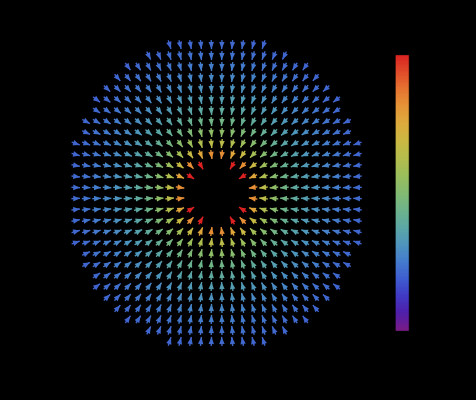

```mathematica
ClearAll["Global`*"]
a = 20;
b = 100;
Subscript[V, 0] = 100;

f = TransformedField["Polar"-> "Cartesian",{(-Subscript[V, 0])/Log[b/a] 1/r,0},{r,θ}-> {x,y}];

cylindersPlot = VectorPlot[Boole[x^2+y^2>a^2&&x^2+y^2<b^2]{Evaluate[f]},{x,-b,b},{y,-b,b},
VectorScale->{0.02,Automatic,None},
VectorPoints->30,
VectorColorFunctionScaling->True,
VectorColorFunction->"Rainbow",
PlotLegends->BarLegend[{"Rainbow",{Subscript[V, 0]/Log[b/a] 1/b,Subscript[V, 0]/Log[b/a] 1/a}}], 
Background->Black, 
PerformanceGoal->"Quality"];

Show[cylindersPlot]
```

# Cylinders Numerical Solution

```mathematica
ClearAll["Global`*"]

data = Import["electricField.dat","Table"];
coords = data[[All,{1,2}]];
comps = data[[All,{3,4}]];
out = Thread[{coords,comps}];

eField = ListVectorPlot[out,
VectorScale->{0.02,Automatic,None},
VectorPoints->{25,12},
VectorColorFunctionScaling->True,
VectorColorFunction->"Rainbow",
PlotLegends->BarLegend[{"Rainbow"}], 
Background->Black, 
PerformanceGoal->"Quality",
AspectRatio->1/2
]
```

# Parallel Plates Analytical Solution

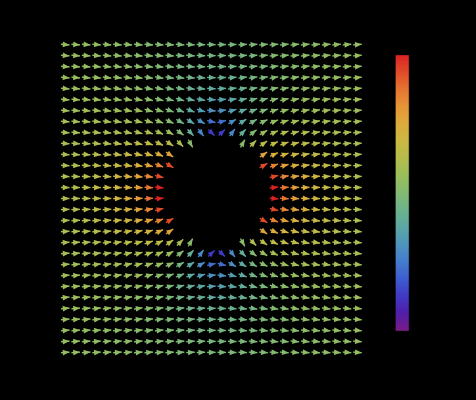

```mathematica
ClearAll["Global`*"]
a = 35; (* radius of the cylinder*)
Subscript[V, 0]= 100;
d = 100;
Subscript[E, 0] = Subscript[V, 0]/d; (* Electric field without cylinder *)
maxE = 2 Subscript[E, 0]; (*Maximum electric field magnitude*)
minE = 0; (*Minimum electric field value *)

g = TransformedField["Polar"-> "Cartesian",{-Subscript[E, 0](-a^2/r^2-1)Cos[θ],Subscript[E, 0](a^2/r^2-1)Sin[θ]},{r,θ}-> {x,y}];

platesPlot = VectorPlot[Boole[x^2+y^2>a^2]{Evaluate[g]},{x,-100,100},{y,-100,100},
VectorScale->{0.02,Automatic,None},
VectorPoints->30,
VectorColorFunctionScaling->True,
VectorColorFunction->"Rainbow",
PlotLegends->BarLegend[{"Rainbow",{minE,maxE}}], 
Background->Black, 
PerformanceGoal->"Quality"];

Show[platesPlot]
```

# Parallel Plates Numerical Solution

```mathematica
ClearAll["Global`*"]
```

# Gas Electron Multiplier